```mathematica
Quit[];
```

```mathematica
ScalarMasslessF0[s_]:=Log[-1/(π s)]+2;
ScalarMasslessF1[s_]:=Log[-1/(π s)]+2+2π×ⅈ;
```

```mathematica
ScalarF0[m_,s_]:=2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
ScalarF1[m_,s_]:=2-2Log[m]+(2 √(4 m^2-s))/(√s)(ArcTan[-(√s)/(√(4 m^2-s))]+π);
```

```mathematica
PropagatorMassless[Mpole_,s_]:=1/(s-Mpole^2-Im[Mpole^2]/Im[ScalarMasslessF1[Mpole^2]](ScalarMasslessF0[s]-ScalarMasslessF1[Mpole^2]));
Propagator[Mpole_,m_,s_]:=1/(s-Mpole^2-Im[Mpole^2]/Im[ScalarF1[m,Mpole^2]](ScalarF0[m,s]-ScalarF1[m,Mpole^2]));
```

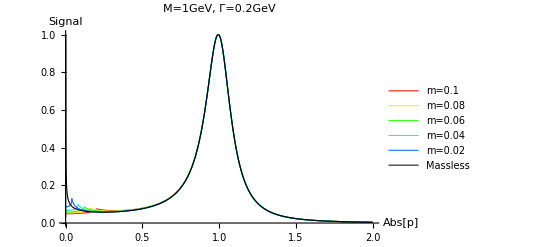

```mathematica
Plot[Evaluate[Append[Table[Abs[Propagator[1-0.1ⅈ,0.02n,p^2]/Propagator[1-0.1ⅈ,0.02n,1-0.1^2]]^2,{n,5,1,-1}],Abs[PropagatorMassless[1-0.1ⅈ,p^2]/PropagatorMassless[1-0.1ⅈ,1-0.1^2]]^2]],{p,0,2},PlotRange->All,PlotStyle->Append[Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,4}],Directive[Black,Thickness[0.002]]],PlotLegends->Placed[Append[Table[StringForm["m=``",0.02n],{n,5,1,-1}],"Massless"],{Right,Top}],PlotLabel->Style["M=1GeV, Γ=0.2GeV",FontSize->18],AxesLabel->{Sqrt[Abs[p^2]],"Signal"},ImageSize->Full,MaxRecursion->15,WorkingPrecision->MachinePrecision]
```

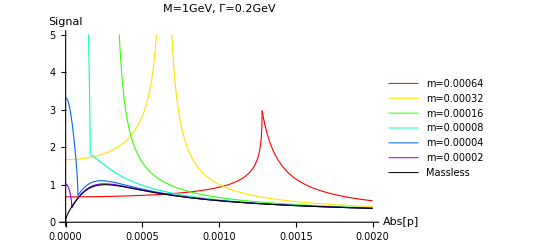

```mathematica
Plot[Evaluate[Append[Table[Abs[Propagator[1-0.1ⅈ,0.00001*2^n,p^2]/Propagator[1-0.1ⅈ,0.00001*2^n,1-0.1^2]]^2,{n,6,1,-1}],Abs[PropagatorMassless[1-0.1ⅈ,p^2]/PropagatorMassless[1-0.1ⅈ,1-0.1^2]]^2]],{p,0,0.002},PlotRange->{0,5},PlotStyle->Append[Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,5}],Directive[Black,Thickness[0.002]]],PlotLegends->Placed[Append[Table[StringForm["m=``",0.00001*2^n],{n,6,1,-1}],"Massless"],{Right,Top}],PlotLabel->Style["M=1GeV, Γ=0.2GeV",FontSize->18],AxesLabel->{Sqrt[Abs[p^2]],"Signal"},ImageSize->Full,MaxRecursion->15,WorkingPrecision->MachinePrecision]
```